```mathematica
ClearAll[iCurvaturePlotHelper, CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#] =!= List &), {t_, tmin_, tmax_}, {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{sol, θ, x, y, if},
  sol = NDSolve[{
     θ'[t] == f,
     x'[t] == Cos[θ[t]],
     y'[t] == Sin[θ[t]],
     θ[tmin] == θ0,
     x[tmin] == x0,
     y[tmin] == y0
     }, {x, y}, {t, tmin, tmax}, opts];
  if = {x[#], y[#]} & /. First[sol];
  if
  ]
CurvaturePlot[f_, {t_, tmin_, tmax_}, opts : OptionsPattern[]] := CurvaturePlot[f, {t, tmin, tmax}, {{0, 0}, 0}, opts]
CurvaturePlot[f_, {t_, tmin_, tmax_}, p : {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{θ, x, y, sol, rlsplot, rlsndsolve, if, ifs},
  rlsplot = FilterRules[{opts}, Options[ParametricPlot]];
  rlsndsolve = FilterRules[{opts}, Options[NDSolve]];
  If[Head[f] === List,
   ifs = iCurvaturePlotHelper[#, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)] & /@ f;
   ParametricPlot[Evaluate[#[tplot] & /@ ifs], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ,
   if = iCurvaturePlotHelper[f, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)];
   ParametricPlot[Evaluate[if[tplot]], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ]
  ]
```

```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_] := Module[{prec = Precision[x], n, p, q, s, tol, w, y, z},
  If[x < 0, Return[0, Module]]; tol = 10^(-prec);
  z = SetPrecision[x, Infinity]; s = 1; y = 0;
  z = If[0 <= z <= 2, 1 - Abs[1 - z],
    q = Quotient[z, 2];
    If[ThueMorse[q] == 1, s = -1];
    1 - Abs[1 - z + 2 q]];
  While[z > 0,
   n = -Floor[RealExponent[z, 2]]; p = 2^n;
   z -= 1/p; w = 1;
   Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
   y = w - y;
   If[Abs[w] < Abs[y] tol, Break[]]];
  SetPrecision[s Abs[y], prec]]
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x]
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &
SetAttributes[FabiusF, {NumericFunction, Listable}];
```

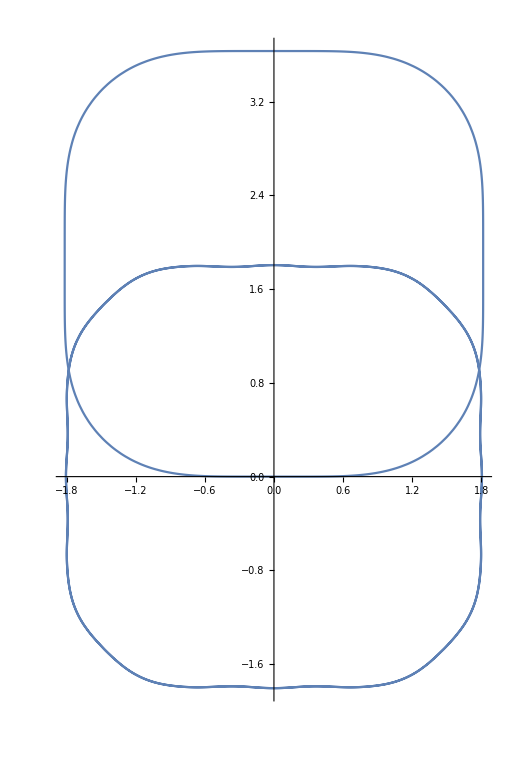

```mathematica
ᔓᔕ={PlotRange-> All,GridLines->{Range[-16,16,1/16],Range[-16,16,1/16]},ImageSize-> 512,MaxRecursion-> 0;PlotPoints-> 1+2^6,WorkingPrecision->10};
(*ᑐᑕꗳᑐᑕ[X_]:={(1+Cos[4*X])};*)
ᑐᑕꗳᑐᑕ[X_]:={(Abs[FabiusF[X/Pi*2]])};
ПꗳП[X_]:=(4*1.625+Abs[FabiusF[X/Pi*4]])/(4*.65+1);
(*ПꗳП[X_]:=(16-Cos[X*4])/(8.25);*)
ᴥ={X,0,4Pi};
Show[
{
CurvaturePlot[Evaluate[ᑐᑕꗳᑐᑕ[X]],Evaluate[ᴥ],Evaluate[ᔓᔕ]]
,
Graphics[PolarPlot[Evaluate[ПꗳП[X]],Evaluate[ᴥ],Evaluate[ᔓᔕ]]]
}
,
Evaluate[ᔓᔕ]
]
```